18018699
1)

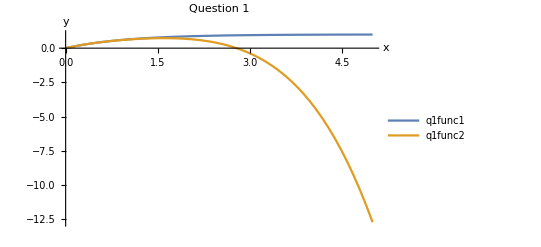

```mathematica
q1func1 = (1-E^(-x));
q1func2 = x - (x^2)/2 + (x^3)/6 - (x^4)/24;
Plot[{q1func1,q1func2},{x, 0, 5}, PlotLabel->"Question 1", AxesLabel->{"x","y"}, PlotLegends->"Expressions", PlotRange->All]
```

```mathematica
2)
```

```mathematica
q2func1 = a x^3 + b x^2 +c x + d == 0;
q2solutions = Solve[q2func1, x];
s1 = q2solutions[[1]]
s2 = q2solutions[[2]]
s3 = q2solutions[[3]]
```

{x→-b/(3 a)-(2^(1/3) (-b^2+3 a c))/(3 a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))+((-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))/(3 2^(1/3) a)}

{x→-b/(3 a)+((1+ⅈ √3) (-b^2+3 a c))/(3 2^(2/3) a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))-((1-ⅈ √3) (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))/(6 2^(1/3) a)}

{x→-b/(3 a)+((1-ⅈ √3) (-b^2+3 a c))/(3 2^(2/3) a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))-((1+ⅈ √3) (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))/(6 2^(1/3) a)}

```mathematica
3)
```

```mathematica
PolyhedronData["Archimedean"]
```

{Cuboctahedron,GreatRhombicosidodecahedron,GreatRhombicuboctahedron,Icosidodecahedron,SmallRhombicosidodecahedron,SmallRhombicuboctahedron,SnubCube,SnubDodecahedron,TruncatedCube,TruncatedDodecahedron,TruncatedIcosahedron,TruncatedOctahedron,TruncatedTetrahedron}